# Setup

### goodlabel

```mathematica
goodlabel::usage="Evaluate[goodlabel[xlabel,ylabel, xstyle, ystyle]] makes plot labels with the desired style. Labels should be passed as strings.";
goodlabel[x_,y_]:={Frame->{{True,False},{True,False}},FrameLabel->{x,y}};
goodlabel[x_,y_,style_]:=goodlabel[x,y,style,style];goodlabel[x_,y_,xstyle_, ystyle_]:={Frame->{{True,False},{True,False}},FrameLabel->{Style[x,xstyle],Style[y,ystyle]}};
```

## sims

```mathematica
sims = SemanticImport[FileNameJoin[{NotebookDirectory[],"aggregated_mh_data.txt"}]];
```

```mathematica
sims=sims[All,<|#,"dhomLow"->#hom-#homLow,"dhomHigh"->#homHigh-#hom|>&];
```

```mathematica
sims
```

Dataset[<>]

```mathematica
αlist = sims[All,#alpha&]//DeleteDuplicates//Normal//Sort;coallist = sims[All,#coal&]//DeleteDuplicates//Normal//Sort;
μlist = sims[All,#mu&]//DeleteDuplicates//Normal//Sort;
```

```mathematica
cdfsims = SemanticImport[FileNameJoin[{NotebookDirectory[],"aggregated_cdf_data.txt"}]];
```

```mathematica
cdfsims=cdfsims [All,<|#,"dcdfLow"->#cdf-#cdfLow,"dcdfHigh"->#cdfHigh-#cdf|>&];
```

```mathematica
sims[#alpha]
```

## functions

```mathematica
fLT[x_,μ_, α_, Dα_]:=NIntegrate[(Cos[k x]/π)/(μ+ Dα k^α),{k,0,∞}];
fLT[x_,μ_, α_]:=fLT[x,μ,α,250^α/2];
```

```mathematica
coeff[c_,μ_,α_,Dα_]:=1/(2/c+(μ/Dα)^(1/α)/(α Sin[π/α]μ));
coeff[c_,μ_,α_]:=coeff[c,μ,α,250^α/2];
```

```mathematica
xscale[μ_,α_,Dα_]:=(Dα/μ)^(1/α);
xscale[μ_,α_]:=xscale[μ,α,250^α/2];
```

```mathematica
xscaleGENERAL[μ_,α_,scaleparameter_]:=xscale[μ,α,scaleparameter^α/2];
```

```mathematica
homscale[coal_,μ_,α_,Dα_]:=(1/π)/(Csc[π/α]/α+ 2 (Dα/μ)^(1/α)μ/coal);
homscale[coal_,μ_,α_]:=homscale[coal,μ,α,250^α/2];
```

```mathematica
approxhomscale[coal_,μ_,α_,Dα_]:=coal/(2 π(Dα/μ)^(1/α)μ);
approxhomscale[coal_,μ_,α_]:=approxhomscale[coal,μ,α,250^α/2];
```

```mathematica
approxhomscaleGENERAL[coal_,μ_,α_, c_]:=approxhomscale[coal,μ,α,c^α/2];
```

```mathematica
Series[homscale[1/ρ,μ,α,Dα],{α,1,1}]
```

(α-1)+O[α-1]^2

```mathematica
exphom[x_,coal_,μ_,Dα_:250^2/2]:=Exp[-√(μ/Dα)x]/(1+4√(μ Dα)/coal)
```

```mathematica
xlist=10^Range[-6,3.5,.25];
```

```mathematica
xlist
```

{1.×10^-6,1.77828×10^-6,3.16228×10^-6,5.62341×10^-6,0.00001,0.0000177828,0.0000316228,0.0000562341,0.0001,0.000177828,0.000316228,0.000562341,0.001,0.00177828,0.00316228,0.00562341,0.01,0.0177828,0.0316228,0.0562341,0.1,0.177828,0.316228,0.562341,1.,1.77828,3.16228,5.62341,10.,17.7828,31.6228,56.2341,100.,177.828,316.228,562.341,1000.,1778.28,3162.28}

```mathematica
intvals=Quiet[Association@@Table[α->Association@@Table[x->NIntegrate[Cos[k x]/(1+k^α),{k,0,∞}],{x,xlist}],{α,αlist⟦;;-2⟧}]];
```

```mathematica
xmaxes=AssociationThread[αlist,{6400,6400,6400,6400, 6400}];
```

```mathematica
xmaxes
```

<|1.→6400,1.1→6400,1.2→6400,1.8→6400,1.82→6400|>

# Plots

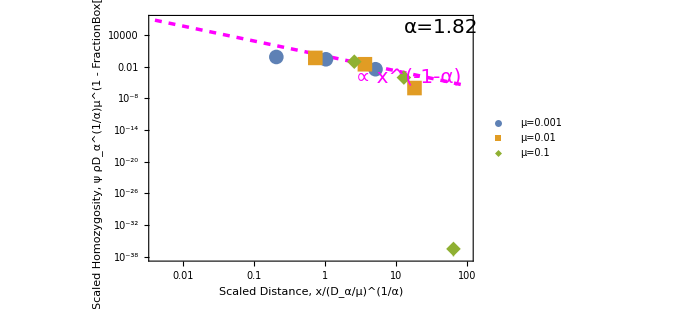

```mathematica
Module[{α=1.82,coal =1, scaleparam = 20, plotpoints,μvals=μlist⟦;;3⟧},plotpoints =Table[{(#x0)/xscaleGENERAL[#mu,#alpha,#c],Around[#hom,{#dhomLow,#dhomHigh}]/approxhomscaleGENERAL[#coal,#mu,#alpha, #c]}&/@sims[Select[#c==  scaleparam && #alpha == α && #coal==coal && #mu ==μ&&#x0>0&& #x0> 100&]],{μ,μvals}];
Show[ListLogLogPlot[Table[{x,intvals[α][x]},{x,Select[xlist,#≤xmaxes[α]&]}],Joined->True,PlotStyle->{Black,Thickness[.01]}
,PlotRange->{{10^-8,20},{10^-3,10^3.5}}],
LogLogPlot[x^(-1-α),{x,.004,100},PlotStyle->{Magenta,Dashed,Thickness[.005]}],
ListLogLogPlot[plotpoints,PlotMarkers->{Automatic,15},IntervalMarkersStyle-><|"WhiskerStyle"->Thick,"FenceStyle"->Thick|>,PlotLegends->Placed[Style["μ="<>ToString[#],20]&/@μvals,{.2,.3}]],Epilog->{Text[Style["α=1.82",20],Scaled[{.9,.95}]],Text[Style["∝ x^(-1-α)",Magenta,20],Scaled[{.8,.75}]]},goodlabel["Scaled Distance, x/(D_α/μ)^(1/α)","Scaled Homozygosity, ψ ρD_α^(1/α)μ^(1 - FractionBox[1, α])",20],FrameStyle->Directive[20,Black], ImageSize->500,
PlotRange->All,Axes->False]]
```

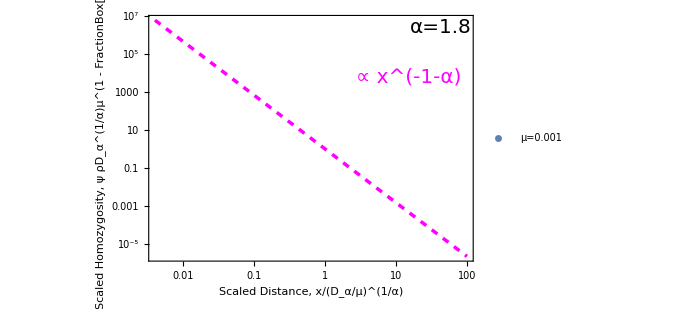

```mathematica
Module[{α=1.82,coal =1, scaleparam = 20, plotpoints,μvals=μlist⟦;;2⟧},plotpoints =Table[{(#x0)/xscaleGENERAL[#mu,#alpha,#c],Around[#hom,{#dhomLow,#hdomHigh}]/approxhomscaleGENERAL[#coal,#mu,#alpha, #c]}&/@sims[Select[#c==  scaleparam && #alpha == α && #coal==coal && #mu ==μ&&#x0>0&]],{μ,μvals}];
Show[ListLogLogPlot[Table[{x,intvals[α][x]},{x,Select[xlist,#≤xmaxes[α]&]}],Joined->True,PlotStyle->{Black,Thickness[.01]},PlotRange->{{10^-8,20},{10^-3,10^3.5}}],
LogLogPlot[x^(-1-α),{x,.004,100},PlotStyle->{Magenta,Dashed,Thickness[.005]}],
ListLogLogPlot[plotpoints,PlotMarkers->{Automatic,15},IntervalMarkersStyle-><|"WhiskerStyle"->Thick,"FenceStyle"->Thick|>,PlotLegends->Placed[Style["μ="<>ToString[#],20]&/@μvals,{.2,.3}]],Epilog->{Text[Style["α=1.8",20],Scaled[{.9,.95}]],Text[Style["∝ x^(-1-α)",Magenta,20],Scaled[{.8,.75}]]},goodlabel["Scaled Distance, x/(D_α/μ)^(1/α)","Scaled Homozygosity, ψ ρD_α^(1/α)μ^(1 - FractionBox[1, α])",20],FrameStyle->Directive[20,Black], ImageSize->500,
PlotRange->All,Axes->False]]
```

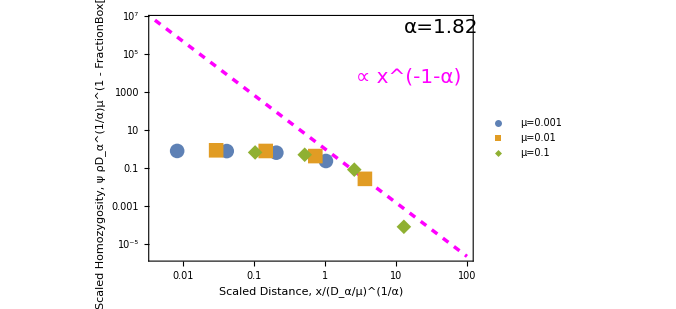

```mathematica
Module[{α=1.82,coal =1, scaleparam = 20, plotpoints,μvals=μlist⟦;;3⟧},plotpoints =Table[{(#x0)/xscaleGENERAL[#mu,#alpha,#c],(#hom)/approxhomscaleGENERAL[#coal,#mu,#alpha, #c]}&/@sims[Select[#c==  scaleparam && #alpha == α && #coal==coal && #mu ==μ&&#x0>0 &&#x0<3000&]],{μ,μvals}];
Show[ListLogLogPlot[Table[{x,intvals[α][x]},{x,Select[xlist,#≤xmaxes[α]&]}],Joined->True,PlotStyle->{Black,Thickness[.01]}
,PlotRange->{{10^-8,20},{10^-3,10^3.5}}],
LogLogPlot[x^(-1-α),{x,.004,100},PlotStyle->{Magenta,Dashed,Thickness[.005]}],
ListLogLogPlot[plotpoints,PlotMarkers->{Automatic,15},IntervalMarkersStyle-><|"WhiskerStyle"->Thick,"FenceStyle"->Thick|>,PlotLegends->Placed[Style["μ="<>ToString[#],20]&/@μvals,{.2,.3}]],Epilog->{Text[Style["α=1.82",20],Scaled[{.9,.95}]],Text[Style["∝ x^(-1-α)",Magenta,20],Scaled[{.8,.75}]]},goodlabel["Scaled Distance, x/(D_α/μ)^(1/α)","Scaled Homozygosity, ψ ρD_α^(1/α)μ^(1 - FractionBox[1, α])",20],FrameStyle->Directive[20,Black], ImageSize->500,
PlotRange->All,Axes->False]]
```

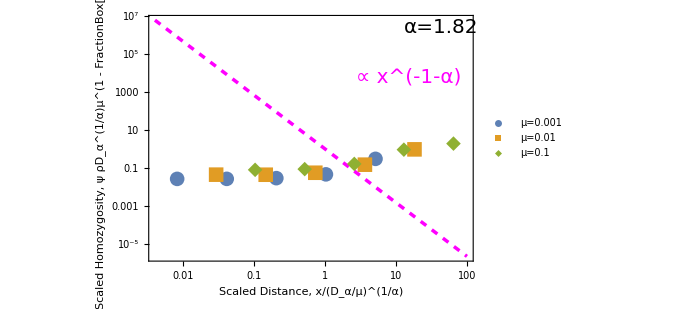

```mathematica
Module[{α=1.82,coal =1, scaleparam = 20, plotpoints,μvals=μlist⟦;;3⟧},plotpoints =Table[{(#x0)/xscaleGENERAL[#mu,#alpha,#c],(#homHigh - #homLow)/(#hom)}&/@sims[Select[#c==  scaleparam && #alpha == α && #coal==coal && #mu ==μ&&#x0>0 &&#x0<5000&]],{μ,μvals}];
Show[ListLogLogPlot[Table[{x,intvals[α][x]},{x,Select[xlist,#≤xmaxes[α]&]}],Joined->True,PlotStyle->{Black,Thickness[.01]}
,PlotRange->{{10^-8,20},{10^-3,10^3.5}}],
LogLogPlot[x^(-1-α),{x,.004,100},PlotStyle->{Magenta,Dashed,Thickness[.005]}],
ListLogLogPlot[plotpoints,PlotMarkers->{Automatic,15},IntervalMarkersStyle-><|"WhiskerStyle"->Thick,"FenceStyle"->Thick|>,PlotLegends->Placed[Style["μ="<>ToString[#],20]&/@μvals,{.2,.3}]],Epilog->{Text[Style["α=1.82",20],Scaled[{.9,.95}]],Text[Style["∝ x^(-1-α)",Magenta,20],Scaled[{.8,.75}]]},goodlabel["Scaled Distance, x/(D_α/μ)^(1/α)","Scaled Homozygosity, ψ ρD_α^(1/α)μ^(1 - FractionBox[1, α])",20],FrameStyle->Directive[20,Black], ImageSize->500,
PlotRange->All,Axes->False]]
```